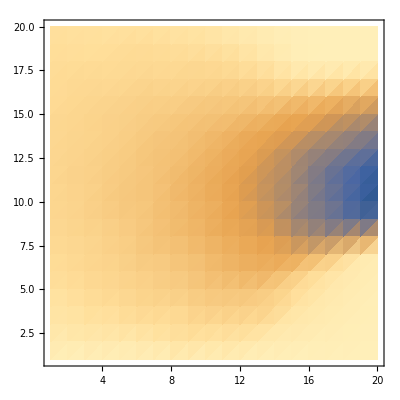

```mathematica
SetDirectory[NotebookDirectory[]];
p=Flatten[ReadList["chirality-data.txt",Number,RecordLists-> True]];
chirality=Table[p[[20*(i-1)+j]],{i,1,20,1},{j,1,20}];
ListDensityPlot[chirality]
```

```mathematica
chirality[[1,1]]
```

-4.45078802108764648

```mathematica
Dimensions[p]
```

{400}

```mathematica
p[[1]]
```

-4.45078802108764648

Part::partw: Part 2 of {{-4.45078802108764648,5.29005146026611328,3.64456486701965332,-1.52323949337005615,«43»,-46.2570075988769531,-69.7319793701171875,-56.1038856506347656,«350»}} does not exist.

Part::partw: Part 3 of {{-4.45078802108764648,5.29005146026611328,3.64456486701965332,-1.52323949337005615,«43»,-46.2570075988769531,-69.7319793701171875,-56.1038856506347656,«350»}} does not exist.

Part::partw: Part 4 of {{-4.45078802108764648,5.29005146026611328,3.64456486701965332,-1.52323949337005615,«43»,-46.2570075988769531,-69.7319793701171875,-56.1038856506347656,«350»}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
Dimensions[chirality]
```

{20,20}

```mathematica
ListDensityPlot[chirality]
```

Part::partw: Part 2 of {{-4.450788021087646,5.290051460266113,3.644564867019653,-1.523239493370056,-4.717601776123047,-4.697031497955322,«40»,-46.97221755981445,-46.25700759887695,-69.73197937011719,-56.10388565063477,«350»}} does not exist.

Part::partw: Part 3 of {{-4.450788021087646,5.290051460266113,3.644564867019653,-1.523239493370056,-4.717601776123047,-4.697031497955322,«40»,-46.97221755981445,-46.25700759887695,-69.73197937011719,-56.10388565063477,«350»}} does not exist.

Part::partw: Part 4 of {{-4.450788021087646,5.290051460266113,3.644564867019653,-1.523239493370056,-4.717601776123047,-4.697031497955322,«40»,-46.97221755981445,-46.25700759887695,-69.73197937011719,-56.10388565063477,«350»}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ListDensityPlot::arrayerr: {«1»} must be a valid array.

Part::partw: Part 2 of {{-4.45078802108764648,5.29005146026611328,3.64456486701965332,-1.52323949337005615,«43»,-46.2570075988769531,-69.7319793701171875,-56.1038856506347656,«350»}} does not exist.

Part::partw: Part 3 of {{-4.45078802108764648,5.29005146026611328,3.64456486701965332,-1.52323949337005615,«43»,-46.2570075988769531,-69.7319793701171875,-56.1038856506347656,«350»}} does not exist.

Part::partw: Part 4 of {{-4.45078802108764648,5.29005146026611328,3.64456486701965332,-1.52323949337005615,«43»,-46.2570075988769531,-69.7319793701171875,-56.1038856506347656,«350»}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ListDensityPlot::arrayerr: {«1»} must be a valid array.

ListDensityPlot[{1}]
 |  |  |  |

```mathematica
Dimensions[p]
```

{1,400}

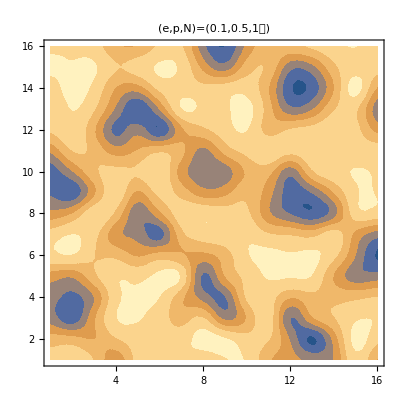

-Graphics3D-

```mathematica
Needs["VectorFieldPlots`"];
SetDirectory[NotebookDirectory[]];
p=ReadList["theta6.txt",Number,RecordLists-> True];
q=ReadList["phi6.txt",Number,RecordLists-> True];
L=18;
p2=Table[{Sin[p[[1,L*(i-1)+j]]]*Cos[q[[1,L*(i-1)+j]]],Sin[p[[1,L*(i-1)+j]]]*Sin[q[[1,L*(i-1)+j]]],Cos[p[[1,L*(i-1)+j]]]},{i,1,L,1},{j,1,L,1}];
edge=1;
chirality=Table[p2[[i,j]].(
     Cross[p2[[i+1,j]],p2[[i,j+1]]]
+Cross[p2[[i-1,j+1]],p2[[i-1,j]]]
+Cross[p2[[i,j+1]],p2[[i,j-1]]]
+Cross[p2[[i-1,j]],p2[[i-1,j-1]]]
+Cross[p2[[i,j-1]],p2[[i+1,j-1]]]
+Cross[p2[[i+1,j+1]],p2[[i,j+1]]]
+Cross[p2[[i-1,j+1]],p2[[i-1,j]]]
+Cross[p2[[i-1,j-1]],p2[[i,j-1]]]
+Cross[p2[[i+1,j-1]],p2[[i+1,j]]]),{i,1+edge,L-edge},{j,1+edge,L-edge}];
ListContourPlot[chirality,PlotLabel->Style["(e,p,N)=(0.1,0.5,1만)",FontSize->20],FrameTicksStyle->Directive[FontOpacity->0,FontSize->0], ContourStyle->None,InterpolationOrder->2]

coord =Flatten[Table[{x,y},{x,1,L,1},{y,1,L,1}],1];
CONFnewlist=Table[{{coord[[i]][[1]],coord[[i]][[2]],0},Flatten[p2,1][[i]]},{i,L*L}];
ListVectorFieldPlot3D[CONFnewlist,ScaleFactor->1,VectorHeads->True]
```

```mathematica
Needs["VectorFieldPlots`"]
R=5;L=20;
Xini = -L-0.5; Xfin = L+0.5;
Yini = -L-0.5; Yfin = L+0.5;

p=Table[{(-2R y)/(x^2 + y^2 + R^2),(2 R x)/(x^2 + y^2 + R^2),(x^2 + y^2 - R^2)/(x^2 + y^2 + R^2)},{x,Xini,Xfin,1},{y,Yini,Yfin,1}];
coord =Flatten[Table[{x,y},{x,Xini,Xfin,1},{y,Yini,Yfin,1}],1];

SIZE = Length[p];
CONFnewlist=Table[{{coord[[i]][[1]],coord[[i]][[2]],0},Flatten[p,1][[i]]},{i,SIZE*SIZE}];
ListVectorFieldPlot3D[CONFnewlist,ScaleFactor->1,VectorHeads->True]
```

-Graphics3D-